# QKT

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[12];
```

```mathematica
Names["QKT`*"]
```

{ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,CompileLevelCounter,CompileSFF,ComputeSigma2Sliding,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,IntWignerCOE,IPR,LengthSpectrum,MeanLevelSpacingRatio,NNSpacings,ParitySectorIndices,PoolSpacingRatios,PoolSpacings,PrCOE,PrCUE,PrPoisson,RandomCOESpectrum,SingleSFF,SingleSpectrumSigma2,UnfoldLinear,ValidateUnfolding,WignerCOE}

```mathematica
Clear[SplitQKTParity];
SplitQKTParity[Op_?MatrixQ]:=Module[{dim,Jval,OpEven,OpOdd},
(*Calculate J from the dimension of the matrix (dim=2J+1)*)
dim=Length[Op];
Jval=(dim-1)/2;
If[EvenQ[Jval],
(*If J is EVEN:Row 1 (M=J) is Even Parity*)
OpEven=Op[[1;; ;;2,1;; ;;2]];
OpOdd=Op[[2;; ;;2,2;; ;;2]];,
(*If J is ODD:Row 1 (M=J) is Odd Parity*)
OpEven=Op[[2;; ;;2,2;; ;;2]];
OpOdd=Op[[1;; ;;2,1;; ;;2]];];
{OpEven,OpOdd}];
```

## QKT

```mathematica
(*Floquet parameters*)
J=500;
α=0.84;
k=3.0;
```

```mathematica
(*Generates all J operators, Jx, Jy, Jz, Jx^2*)
ops=generateSpinOperators[J];
```

```mathematica
?GetQKTParityEigensystem
```

```mathematica
data=GetQKTParityEigensystem[J,α,k];
```

```mathematica
{eigenvalM,eigenvalm}={data["Even","Quasienergies"],data["Odd","Quasienergies"]};
{neweigenvecM,neweigenvecm}={data["Even","FullVectors"],data["Odd","FullVectors"]};
```

```mathematica
{MeanLevelSpacingRatio[Sort[Arg[eigenvalM]]],MeanLevelSpacingRatio[Sort[Arg[eigenvalm]]]}
```

{0.449867,0.439721}

```mathematica
(*Unfolding, only works for uniform density of states in the chaotic regime COE*)
phases=Sort[Arg[eigenvalM]];
n=Length[phases];
unfolded=phases*(n/(2*Pi));
spacings=Differences[unfolded];
meanSpacing=Mean[spacings];
spacings=spacings/meanSpacing;
```

```mathematica
poisson[s_]:=Exp[-s];
wignerDyson[s_]:=(Pi*s/2)*Exp[-(Pi*s^2)/4];
```

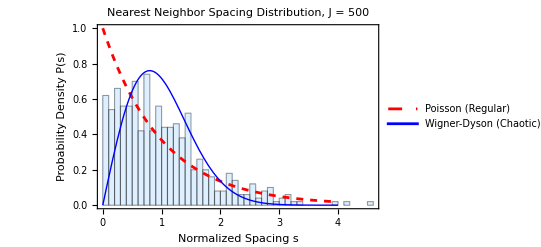

```mathematica
Show[Histogram[spacings,{0.1},"PDF",ChartStyle->LightBlue,Frame->True,FrameLabel->{"Normalized Spacing s","Probability Density P(s)"},PlotLabel->"Nearest Neighbor Spacing Distribution, J = "<>ToString[J]],Plot[{poisson[s],wignerDyson[s]},{s,0,4},PlotStyle->{{Red,Dashed},{Blue,Thick}},PlotLegends->{"Poisson (Regular)","Wigner-Dyson (Chaotic)"}]]
```

## IPR & Husimis

```mathematica
(*Resolution of the grid for the phase space*)
radius=2;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPointsRaw=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
(*Keep only those inside disk*)
region=Select[gridPointsRaw,Norm[#]<radius&];
region//Dimensions
```

{20069,2}

```mathematica
Print["Generating coherent states over ",Length[region]," points..."];
coherentStateGenerator=generateCoherentStateCompiler[];
statesCompiled=ParallelMap[coherentStateGenerator[J,#[[1]],#[[2]]]&,region,Method->"CoarsestGrained"  (*Optional:better batching*)];
```

Generating coherent states over 20069 points...

```mathematica
(*Sorting with respect the average energy*)
ae=Chop[Map[#.Vop.ConjugateTranspose[#]&,neweigenvec]];
```

```mathematica
ordering=Ordering[ae];
(*Sort eigenvectors and expectations accordingly*)
eigenvecsSorted=neweigenvec[[ordering]];
eigenvalSorted=neweigenval[[ordering]];
```

```mathematica
Print["Projecting states into Floquet basis..."];
overlaps=Conjugate[eigenvecsSorted].Transpose[statesCompiled];
Print["Computing IPRs..."];
iprCompiled=Total[Abs[overlaps]^4,{1}];
```

Projecting states into Floquet basis...

Computing IPRs...

```mathematica
newdata=Table[-Log[i]/Log[2 J+1],{i,iprCompiled}];
```

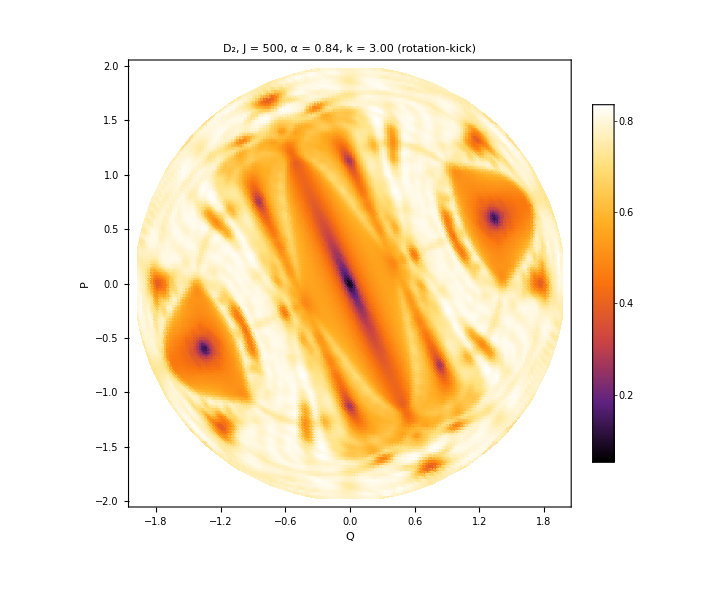

```mathematica
plot=ListDensityPlot[Transpose[{region[[All,1]],region[[All,2]],newdata}],PlotRange->All,PlotTheme->"Detailed",ColorFunction->"SunsetColors",PlotLabel->Style["D₂, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>" (rotation-kick)",25,Black],ImageSize->600,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,Background->White]
```

```mathematica
dir="HusimiPlots";
If[!DirectoryQ[dir],CreateDirectory[dir]];
```

```mathematica
husimiValues=Abs[overlaps]^2;
husimiValuesSorted=husimiValues;
```

```mathematica
(*Set parameters, 2J+1 Husimis in total*)
numEigenstates=2J+1; 
plots=Table[
Module[{husimiList,plot},
husimiList=MapThread[Append,{region,husimiValuesSorted[[q]]}];
plot=ListDensityPlot[husimiList,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["AE Husimi, J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[NumberForm[k,{4,2}]]<>", Eigenvec_q = "<>ToString[q],25,Black],ImageSize->1000,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90 Degree]},LabelStyle->Directive[30,Black],AspectRatio->1,Frame->True,InterpolationOrder->1];
Export[FileNameJoin[{dir,"AE_Husimi_J_"<>ToString[J]<>"_q"<>ToString[q]<>".png"}],plot];
plot],{q,numEigenstates}];
```

```mathematica
ae//Sort
```

{-23.7541,-15.6602,-10.8053,-9.90192,-5.64294,-2.39631,0.109928,2.07873,2.16826,2.43,2.98262,2.98384,3.66659,3.88743,3.88746,4.61932,4.61933,5.12387,5.20698,5.20699,5.6674,5.6677,6.00415,6.01507,6.17422,6.28965,6.2964,6.36884,6.59838,6.62782,6.84551,7.46039,8.60166,9.62781,10.7949,12.2561,14.1865,15.5611,16.8202,20.5642,26.1252}

# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Github\\Chaotic_eigenfunctions\\Geometric floquet\\QKT_full.wl"];
```

```mathematica
LaunchKernels[12]
```

```mathematica
Names["QKT`*"]
```

{ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,CompileLevelCounter,CompileSFF,ComputeSigma2Sliding,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,IntWignerCOE,IPR,LengthSpectrum,MeanLevelSpacingRatio,NNSpacings,ParitySectorIndices,PoolSpacingRatios,PoolSpacings,PrCOE,PrCUE,PrPoisson,RandomCOESpectrum,SingleSFF,SingleSpectrumSigma2,UnfoldLinear,ValidateUnfolding,WignerCOE}

## Computations

```mathematica
(*Execution*)
α=0.84;
k=3.;
kicks=2000;
(*Random inintial conditions on the disk/phase space*)
points=300;
randomregion=RandomPoint[Disk[{0,0},1.99],points];
```

```mathematica
(*The'Listable' attribute handles the parallel iteration over'randomregion' automatically*)
result=ClassicalMapeo[randomregion,α,k,kicks,0];
```

```mathematica
newpoincarea=ArrayReshape[result,{points*kicks,2}];
poincare=ListPlot[newpoincarea,PlotStyle->Directive[PointSize[0.0005],Black,Opacity[0.15]],PlotLabel->Row[{Style["α = ",35,Black],Style[N[α],35,Black],Style[", k = ",35,Black], Style[N[k],35,Black],Style[" (rotation-kick)",24,Black]}],FrameLabel->{Style["Q",30,Black],Rotate[Style["P",30,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,PlotRange->{{-2,2},{-2,2}},ImageSize->1000]
```

-Graphics-

```mathematica
Export["poincareplot.png",poincare,ImageResolution->300]
```

poincareplot.png

# Powers

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-0  SETUP: parameters, chart, one-step map                                *)
(* ---------------------------------------------------------------------------- *)

alpha = 0.84;
k     = 20.0;      (* fully chaotic regime, same as Figs. 2-3 of your report *)
p     = 5000;      (* default burst length *)

(* Chart between the unit sphere (x,y,z) and the (Q,P) disk of radius 2.
   Conventions: Sz = (Q^2+P^2)/2 - 1  (origin = south pole, boundary = north pole),
   Sx = Q Sqrt[4-Q^2-P^2]/2 , Sy = P Sqrt[4-Q^2-P^2]/2.
   If your quantum plots appear mirrored in P, flip the sign of Sy here:
   that is only the orientation convention of the coherent-state chart.        *)
toSphere[{Q_, P_}] := With[{s = Sqrt[4. - Q^2 - P^2]}, {Q s/2, P s/2, (Q^2 + P^2)/2 - 1}];
toDisk[{x_, y_, z_}] := Sqrt[2./(1. - Min[z, 1. - 10.^-12])] {x, y};   (* clipped at the north pole *)

(* The one-step map: kick by k*Sx about the x-axis, then precession alpha about z. *)
Rz[a_] := RotationMatrix[a, {0, 0, 1}];
Rx[a_] := RotationMatrix[a, {1, 0, 0}];
Fmat[x_] := Rz[alpha].Rx[k x[[1]]];    (* the 3x3 rotation ATTACHED TO the point x *)
step[x_] := Fmat[x].x;                 (* the true kicked-top dynamics             *)
```

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-1  AXIS AND ANGLE OF THE ONE-STEP ROTATION                                *)
(*  Every R in SO(3) is a rotation by an angle about an axis. Extract both.     *)
(* ---------------------------------------------------------------------------- *)

angleOf[R_] := ArcCos[Clip[(Tr[R] - 1.)/2., {-1., 1.}]];   (* in [0, Pi] *)
axisOf[R_]  := Normalize[{R[[3,2]] - R[[2,3]], R[[1,3]] - R[[3,1]], R[[2,1]] - R[[1,2]]}];
(* Caveat: axisOf uses the antisymmetric part, which vanishes when the angle is  *)
(* exactly Pi. That happens on the isolated circles Sx = (2m+1) Pi/k (see PP-2). *)
(* Near those circles the axis, hence mu, is numerically noisy AND flips sign.   *)
(* Those thin noisy rings in the plots are chart artifacts of the sign of nHat,  *)
(* not dynamics; plotting Abs[mu] removes the sign ambiguity.                    *)

nHat[x_] := axisOf[Fmat[x]];
th[x_]   := angleOf[Fmat[x]];
mu[x_]   := nHat[x].x;          (* projection on the local axis: the stepwise invariant *)
hEff[x_] := th[x] mu[x];        (* frozen effective Hamiltonian h = theta * (nHat.x)    *)
```

```mathematica
(* Sanity checks (all should be ~ 0): *)
x0 = toSphere[{0.9, 0.4}];
check1 = Norm[Fmat[x0] - RotationMatrix[th[x0], nHat[x0]]]
(* F(x0) IS the rotation by th about nHat -- axis/angle extraction is correct.   *)
check2 = Cos[th[x0]/2] - Abs[Cos[alpha/2] Cos[k x0[[1]]/2]]
(* Closed form for the angle of a product of two rotations about ORTHOGONAL      *)
(* axes: cos(theta/2) = |cos(alpha/2) cos(k Sx/2)|.                              *)
(* Consequence worth internalizing: th depends ONLY on Sx. The geometry of the   *)
(* patterns must therefore come from the AXIS field, i.e. from mu, not from th.  *)
```

6.28503×10^-16

-1.35308×10^-16

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-2  THE SCALAR FIELDS OVER PHASE SPACE                                     *)
(* ---------------------------------------------------------------------------- *)

grid = Select[Flatten[Table[{Q, P}, {Q, -1.99, 1.99, 0.025}, {P, -1.99, 1.99, 0.025}], 1], Norm[#] < 1.99 &];
```

```mathematica
grid//Dimensions
```

{19906,2}

```mathematica
fieldPlot[f_, label_] := ListDensityPlot[{#[[1]], #[[2]], f[toSphere[#]]} & /@ grid,
   PlotLabel -> label, ColorFunction -> "SunsetColors", AspectRatio -> 1,
   Frame -> True, PlotRange -> All, ImageSize -> 420];
```

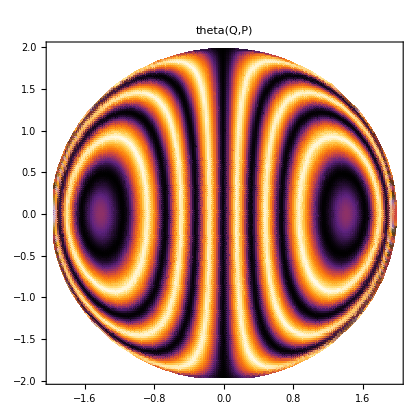

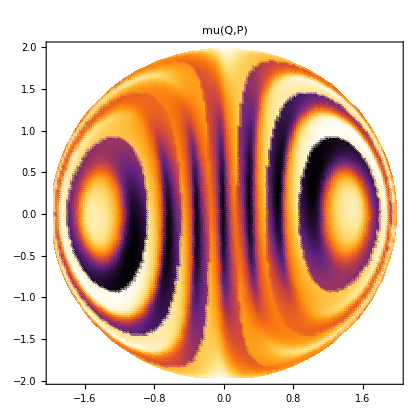

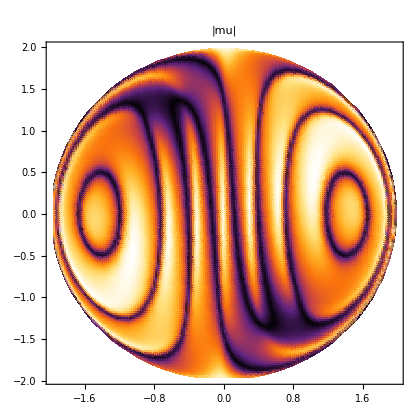

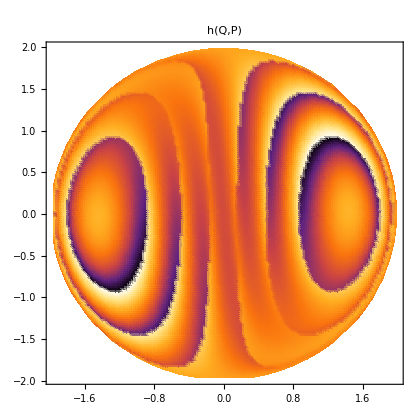

```mathematica
fieldPlot[th, "theta(Q,P)"]        (* expect bands = level sets of Sx only ("lens" curves) *)
fieldPlot[mu, "mu(Q,P)"]           (* the candidate skeleton; note the sign-flip rings     *)
fieldPlot[Abs[mu[#]] &, "|mu|"]    (* same, without the axis-sign ambiguity                *)
fieldPlot[hEff, "h(Q,P)"]          (* theta-weighted version of mu                          *)
```

```mathematica
(* Contour (level-set) versions, used later as overlays: *)
muContours = ListContourPlot[{#[[1]], #[[2]], mu[toSphere[#]]} & /@ grid,
   Contours -> 30, ContourShading -> None, ContourStyle -> Directive[Red, Opacity[0.7]],
   AspectRatio -> 1, Frame -> True];
```

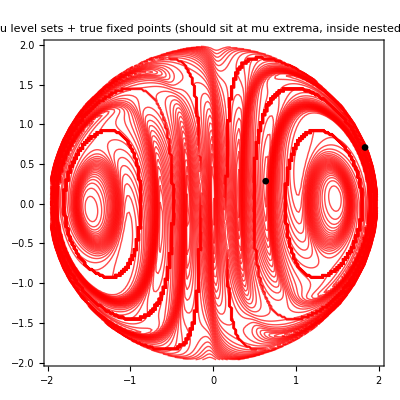

```mathematica
(* Fixed points of the TRUE map are the points lying on their own axis, i.e. the *)
(* extrema mu = +-1. Cheap grid locator for the true fixed points:               *)
fpGuess = Select[grid, Norm[step[toSphere[#]] - toSphere[#]] < 0.02 &];
Show[muContours, ListPlot[fpGuess, PlotStyle -> Directive[Black, PointSize[0.012]]],
   PlotLabel -> "mu level sets + true fixed points (should sit at mu extrema, inside nested loops)"]
```

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-3  ONE FROZEN BURST = ONE CIRCLE                                          *)
(*  Inside a single Poincare-power step the matrix is fixed. Show that the       *)
(*  point cannot leave the circle around nHat(x0), and that nHat(x0).x is        *)
(*  EXACTLY conserved during the burst -- while the true orbit scrambles it.     *)
(* ---------------------------------------------------------------------------- *)

frozenOrbit = NestList[Fmat[x0].# &, x0, 300];   (* SAME matrix every time *)
trueOrbit   = NestList[step, x0, 300];           (* matrix re-evaluated: real dynamics *)

n0 = nHat[x0]; m0 = mu[x0];
e1 = Normalize[x0 - m0 n0]; e2 = Cross[n0, e1];
```

```mathematica
circ3D = ParametricPlot3D[m0 n0 + Sqrt[1 - m0^2] (Cos[t] e1 + Sin[t] e2), {t, 0, 2 Pi},
   PlotStyle -> Directive[Red, Thick]];
```

```mathematica
Show[Graphics3D[{Opacity[0.10], Sphere[]}, Boxed -> False, ImageSize -> 500],
   circ3D,
   Graphics3D[{Blue, PointSize[0.006], Point[frozenOrbit],
               Gray, PointSize[0.004], Point[trueOrbit],
               Black, Arrow[Tube[{{0, 0, 0}, 1.25 n0}, 0.006]]}],
   PlotLabel -> "blue: frozen burst (one circle) / gray: true orbit (chaotic sea) / arrow: nHat(x0)"]
```

-Graphics3D-

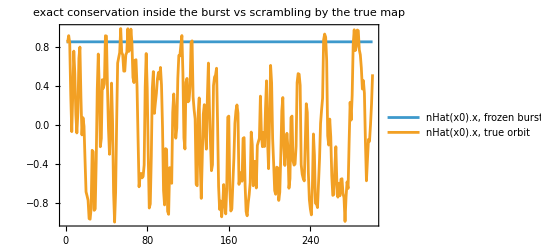

```mathematica
ListLinePlot[{n0.# & /@ frozenOrbit, n0.# & /@ trueOrbit},
   PlotLegends -> {"nHat(x0).x, frozen burst", "nHat(x0).x, true orbit"},
   PlotLabel -> "exact conservation inside the burst vs scrambling by the true map",
   Frame -> True, PlotRange -> All]
```

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-4  THE POINCARE POWER MAP AND THE SLOW DRIFT OF mu                        *)
(*  Between bursts the axis turns a little; mu is no longer exact but should     *)
(*  drift SLOWLY along the orbit -- this is the adiabatic-invariant claim.       *)
(* ---------------------------------------------------------------------------- *)

PP1[x_] := MatrixPower[Fmat[x], p].x;
ppOrbit = NestList[PP1, x0, 400];
```

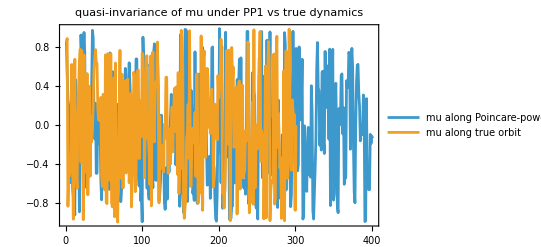

```mathematica
ListLinePlot[{mu /@ ppOrbit, mu /@ trueOrbit[[;; Min[301, Length[trueOrbit]]]]},
   PlotLegends -> {"mu along Poincare-power orbit", "mu along true orbit"},
   PlotLabel -> "quasi-invariance of mu under PP1 vs true dynamics",
   Frame -> True, PlotRange -> All]
```

```mathematica
(* The 'slowly turning circles' picture: draw the local circle at the first     *)
(* few PP iterates. Consecutive circles should be nearly coincident.             *)
circAt[x_] := With[{n = nHat[x], m = mu[x]}, With[{a = Normalize[x - (n.x) n]},
   ParametricPlot3D[m n + Sqrt[1 - m^2] (Cos[t] a + Sin[t] Cross[n, a]), {t, 0, 2 Pi},
      PlotStyle -> Directive[Thick, Hue[0.0]]]]];
Show[Graphics3D[{Opacity[0.08], Sphere[]}, Boxed -> False, ImageSize -> 500],
   Table[circAt[ppOrbit[[j]]], {j, 1, 10}],
   Graphics3D[{Black, PointSize[0.008], Point[ppOrbit[[;; 10]]]}],
   PlotLabel -> "the circle foliation sampled by the first 10 PP steps"]
```

-Graphics3D-

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-5  DENSITY OF THE POINCARE POWER vs LEVEL SETS                            *)
(*  The hypothesis: dark curves in your Fig. 2 = level curves / separatrices of  *)
(*  mu (equivalently of h), plus the theta-stationary circles below.             *)
(*  A partial match is informative too: whatever is NOT matched needs another    *)
(*  mechanism (resonances -> PP-6, or dynamical averaging -> PP-7).              *)
(* ---------------------------------------------------------------------------- *)
seeds = RandomPoint[Disk[{0, 0}, 1.95], 250];
cloud[pp_] := toDisk /@ Flatten[Table[NestList[MatrixPower[Fmat[#], pp].# &, toSphere[s], 250], {s, seeds}], 1];
```

```mathematica
cloudPlot[pp_] := ListPlot[cloud[pp], PlotStyle -> Directive[Blue, Opacity[0.1], PointSize[0.0025]],
   AspectRatio -> 1, Frame -> True, PlotRange -> {{-2, 2}, {-2, 2}},
   PlotLabel -> "Poincare power cloud, p = " <> ToString[pp], ImageSize -> 500];
```

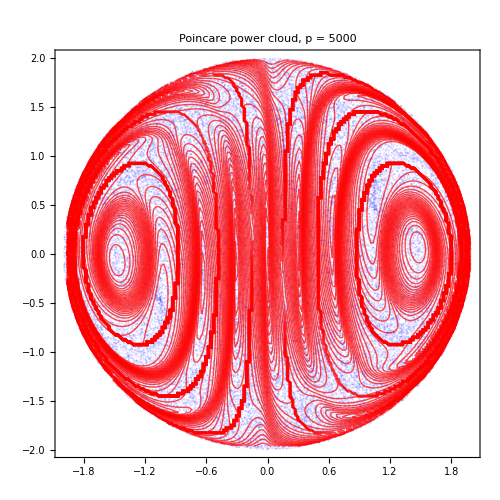

```mathematica
c5000 = cloudPlot[5000];
Show[c5000, muContours]     (* test 1: mu level sets against the density *)
```

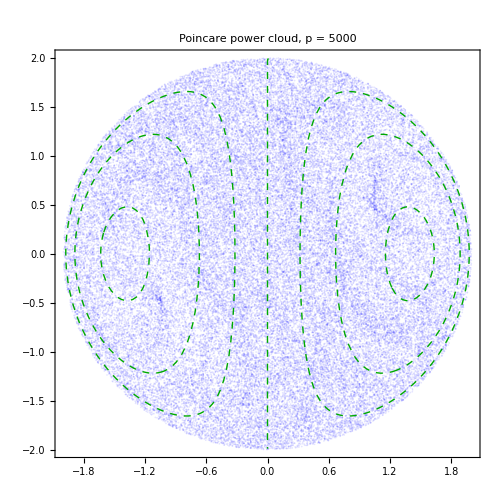

```mathematica
(* Second candidate family of PERSISTENT curves: circles where theta(Sx) is      *)
(* stationary, d theta/d Sx = 0, i.e. Sx = 2 Pi m / k. On these circles the      *)
(* burst angle is locally constant, so near-resonant strips pile up for every p. *)
sxStationary = ContourPlot[q Sqrt[4 - q^2 - pp2^2]/2, {q, -2, 2}, {pp2, -2, 2},
   Contours -> Table[2 Pi m/k, {m, -3, 3}], ContourShading -> None,
   ContourStyle -> Directive[Darker[Green], Dashed], RegionFunction -> (#1^2 + #2^2 < 3.96 &)];
Show[c5000, sxStationary]   (* test 2: theta-stationary circles against the density *)
```

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-6  THE ROLE OF p                                                           *)
(*  Mechanism A (foliation of mu): p-independent once p is large and generic.    *)
(*  Mechanism B (resonance): where p*theta(x) ~ 0 mod 2Pi the burst is           *)
(*  near-identity -> stickiness on curves theta = 2 Pi m / p, which MOVE with p. *)
(*  Since theta = theta(Sx), those curves are constant-Sx lenses. At p ~ 5000    *)
(*  they are so dense they blur into background; at SMALL p they are sparse and  *)
(*  clearly visible, and they visibly migrate when p changes.                    *)
(* ---------------------------------------------------------------------------- *)

(* Near-identity indicator of the burst: [F(x)]^p = rotation by p*theta, which   *)
(* is close to the identity exactly where |sin(p*theta/2)| ~ 0.                  *)
resInd[pp_] := ListDensityPlot[{#[[1]], #[[2]], Abs[Sin[pp th[toSphere[#]]/2.]]} & /@ grid,
   ColorFunction -> "GrayTones", AspectRatio -> 1, Frame -> True,
   PlotLabel -> "|sin(p theta/2)|, p = " <> ToString[pp] <> "  (dark = near-identity burst)", ImageSize -> 420];
```

```mathematica
(* Small p: resonance curves dominate and move with p. Compare cloud vs indicator. *)
GraphicsRow[{cloudPlot[5], resInd[5]}]
GraphicsRow[{cloudPlot[8], resInd[8]}]
GraphicsRow[{cloudPlot[13], resInd[13]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Large, unrelated p: whatever persists across these belongs to the foliation   *)
(* (mu / theta-stationary families), not to any particular resonance.            *)
GraphicsRow[{cloudPlot[2001], cloudPlot[5003], cloudPlot[9973]}]
```

-Graphics-

```mathematica
(* ---------------------------------------------------------------------------- *)
(*  PP-7  PERIOD 2: THE SAME CONSTRUCTION ON THE FROZEN TWO-STEP MONODROMY       *)
(*  M2(x) = F(F(x)x) . F(x) is the product of the one-step matrices along the    *)
(*  TRUE orbit segment of length 2. It is again a single rotation, so it has     *)
(*  its own axis field n2, angle field th2, invariant mu2 = n2.x, and its own    *)
(*  Poincare power. Everything from PP-1..PP-6 transfers with F -> F^2.          *)
(*  (This implements one reading of Eq. (34) of the report; if you intended a    *)
(*  different composition, only the line defining M2 changes.)                   *)
(* ---------------------------------------------------------------------------- *)

M2[x_]  := Fmat[step[x]].Fmat[x];
n2[x_]  := axisOf[M2[x]];
th2[x_] := angleOf[M2[x]];
mu2[x_] := n2[x].x;

(* Sanity checks: *)
check3 = Norm[M2[x0].x0 - step[step[x0]]]
(* one application of the frozen two-step matrix to its base point reproduces    *)
(* the TRUE second iterate exactly.                                              *)
fp2Guess = Select[grid, Norm[step[step[toSphere[#]]] - toSphere[#]] < 0.02 &];
(* period-2 (and period-1) points; they must sit at extrema of mu2, i.e. mu2=+-1 *)
```

2.498×10^-16

```mathematica
fieldPlot[th2, "theta2(Q,P)"]
(* NOTE: unlike th, th2 is NOT a function of Sx alone -- the composition mixes   *)
(* coordinates. The resonance curves of the period-2 power are therefore genuine *)
(* two-dimensional families, richer than the constant-Sx lenses of period 1.     *)
fieldPlot[Abs[mu2[#]] &, "|mu2|"]
```

-Graphics-

-Graphics-

```mathematica
mu2Contours = ListContourPlot[{#[[1]], #[[2]], mu2[toSphere[#]]} & /@ grid,
   Contours -> 30, ContourShading -> None, ContourStyle -> Directive[Purple, Opacity[0.7]],
   AspectRatio -> 1, Frame -> True];

Show[mu2Contours, ListPlot[fp2Guess, PlotStyle -> Directive[Black, PointSize[0.010]]],
   PlotLabel -> "mu2 level sets + fixed points of F^2"]

cloud2[pp_] := toDisk /@ Flatten[Table[NestList[MatrixPower[M2[#], pp].# &, toSphere[s], 250], {s, seeds}], 1];
c2 = ListPlot[cloud2[5000], PlotStyle -> Directive[Blue, Opacity[0.06], PointSize[0.0015]],
   AspectRatio -> 1, Frame -> True, PlotRange -> {{-2, 2}, {-2, 2}},
   PlotLabel -> "period-2 Poincare power cloud, p = 5000", ImageSize -> 500];
Show[c2, mu2Contours]

(* Drift test, period-2 version: *)
pp2Orbit = NestList[MatrixPower[M2[#], p].# &, x0, 400];
ListLinePlot[{mu2 /@ pp2Orbit, mu2 /@ trueOrbit[[;; 301]]},
   PlotLegends -> {"mu2 along period-2 PP orbit", "mu2 along true orbit"},
   PlotLabel -> "quasi-invariance of mu2", Frame -> True, PlotRange -> All]

(* ============================================================================ *)
(*  READING GUIDE                                                               *)
(*  PP-1/2: the two fields exist and theta carries no geometry (Sx only);       *)
(*          the geometry is in the axis field, summarized by mu.                *)
(*  PP-3:   confinement to a circle + exact in-burst conservation. This is      *)
(*          the mechanical core of the whole construction.                      *)
(*  PP-4:   mu drifts slowly under PP1, fast under the true map: mu is a        *)
(*          stepwise adiabatic invariant of the Poincare power, NOT of F.       *)
(*  PP-5:   which dark curves are mu level sets, which are theta-stationary     *)
(*          circles, which are neither (-> those need PP-6/PP-7 or a genuinely  *)
(*          different mechanism).                                               *)
(*  PP-6:   curves that move with p are resonances of that p; curves that       *)
(*          survive unrelated large p belong to the foliation.                  *)
(*  PP-7:   period-2 = identical logic on the two-step monodromy; its           *)
(*          invariant mu2 has extrema on period-2 orbits and its own,           *)
(*          richer level-set family.                                            *)
(* ============================================================================ *)
```

-Graphics-

-Graphics-

-Graphics-